```mathematica
Solve[{v^2+v-u+0==0,2 v-u==0},{u,v}]/.{b->2}//Simplify
```

{{u→0,v→0},{u→2,v→1}}

```mathematica
{{u->1/2 (-b+b^2-b √(1-2 b+b^2-4 d)),v->1/2 (-1+b-s)},{u->1/2 (-b+b^2+b √(1-2 b+b^2-4 d)),v->1/2 (-1+b+√(1-2 b+b^2-4 d))}}
```

```mathematica
Grad[{v^2+v-u+d,b v-u},{u,v}]
```

{{-1,1+2 v},{-1,b}}

```mathematica
Eigenvalues[{{-1,1+2 v},{-1,b}}]
```

{1/2 (-1+b-√(-3+2 b+b^2-8 v)),1/2 (-1+b+√(-3+2 b+b^2-8 v))}

```mathematica
-3+2 b+b^2-8 v/.v->1/2 (-b+b^2-b s)//Simplify
```

-3-3 b^2+b (6+4 s)

```mathematica
Factor[-3-3 b^2+b (6+4 s)]
```

-3+6 b-3 b^2+4 b s

```mathematica
s=√((1-b)^2-4d)
```

√((1-b)^2-4 d)

```mathematica
4b s-3(1-b)^2//Simplify//Expand
```

```mathematica
-4 b √(1-2 b+b^2-4 d)/.{b->2,d->0.21484375}
```

-6.

```mathematica
Solve[(-3+6 b-3 b^2)^2==(4 b √(1-2 b+b^2-4 d))^2,d]
```

{{d→(-9+36 b-38 b^2+4 b^3+7 b^4)/(64 b^2)}}

```mathematica
Reduce[-3+6 b-3 b^2+4 b √(1-2 b+b^2-4 d)==0,d]
```

Reduce::useq: Reduceで求められた解に未解決の方程式{0==-(3 (-1+2 b+√(Power[«2»] Power[«2»]) b-b^2))/(4 b)}が含まれています．これは一式の解がWolfram言語関数の分枝切断線に依存しているためであると考えられます．

b≠0&&0==-(3 (-1+2 b+√((-1+b)^4/b^2) b-b^2))/(4 b)&&d==((-1+b)^2 (-9+18 b+7 b^2))/(64 b^2)

```mathematica
With[{b=2},(-9+36 b-38 b^2+4 b^3+7 b^4)/(64 b^2)//N]
```

0.214844

```mathematica
Solve[-3+6 b-3 b^2-4 b √(1-2 b+b^2-4 d)==0,d]
```

Solve::nongen: 解はパラメータのすべての値に対しては有効ではない可能性があります．

{{d→(-9+36 b-38 b^2+4 b^3+7 b^4)/(64 b^2)}}

```mathematica
-3+6 b-3 b^2+4 b √(1-2 b+b^2-4 d)
```

```mathematica
Point[{u,v}]/.NSolve[#==0&/@F[u,v],{u,v}]
```

{Point[{1.7746,0.887298}],Point[{0.225403,0.112702}]}

```mathematica
Evaluated[Point[{u,v}]/.NSolve[#==0&/@F[u,v],{u,v}]]
```

Evaluated[{Point[{1.7746,0.887298}],Point[{0.225403,0.112702}]}]

```mathematica
F[u_,v_,d_,b_]:={v^2+v-u+d,b v-u}
```

```mathematica
NSolve[#==0&/@F[u,v],{u,v}]
```

{{u→1.7746,v→0.887298},{u→0.225403,v→0.112702}}

```mathematica
Clear[s]
```

```mathematica
T=√((1-b)^2-4 √((1-b)^2-4d))
```

√((1-b)^2-4 √((1-b)^2-4 d))

```mathematica
Reduce[(1-b)^2-4 √((1-b)^2-4d)<0,{b,d}]
```

b∈ℝ&&d<1/64 (15-28 b+10 b^2+4 b^3-b^4)

```mathematica
1/64 (15-28 b+10 b^2+4 b^3-b^4)/.{b->2}
```

15/64

```mathematica
-1+b+T//Simplify
```

-1+b+√(1-2 b+b^2-4 √(1-2 b+b^2-4 d))

```mathematica
Reduce[-1+b-T0,{b,d}]
```

b<1&&1/64 (15-28 b+10 b^2+4 b^3-b^4)≤d≤1/4 (1-2 b+b^2)

```mathematica
Reduce[-1+b+T<0,{b,d}]
```

b<1&&1/64 (15-28 b+10 b^2+4 b^3-b^4)≤d<1/4 (1-2 b+b^2)

```mathematica
-1+b-√(1-2 b+b^2+4 √(1-2 b+b^2-4 d))/.{b->2,d->0.1}
```

-1.02445

```mathematica
Maximize[-1+b+√(1-2 b+b^2-4 √(1-2 b+b^2-4 d)),{b,d}]
```

Maximize::natt: 指定の制約条件を満足するどの点においても，最大値に達していません．

{∞,{b→Indeterminate,d→Indeterminate}}

```mathematica
Maximize[-1+b-√(1-2 b+b^2-4 √(1-2 b+b^2-4 d)),{b,d}]
```

{0,{b→2,d→1/4}}

```mathematica
Reduce[-1+b+√(1-2 b+b^2+4 √(1-2 b+b^2-4 d))<=0,{b,d}]
```

(b==1&&d==0)||(b<1&&d==1/4 (1-2 b+b^2))

```mathematica
Reduce[-1+b+T<=00,d]
```

(b==1&&d==0)||(b<1&&d==1/4 (1-2 b+b^2))

```mathematica
Reduce[-1+b-T==0,d]
```

Reduce::useq: Reduceで求められた解に未解決の方程式{0==-1+b-√(1-2 b+b^2)}が含まれています．これは一式の解がWolfram言語関数の分枝切断線に依存しているためであると考えられます．

0==-1+b-√(1-2 b+b^2)&&d==1/4 (-1+b)^2

```mathematica
Reduce[-1+b-√□]
```

```mathematica
-3+2 bb+bb^2-8 v/.v->1/2 (-1+bb-s)//Simplify
```

1-2 bb+bb^2+4 s

```mathematica
-3+2 bb+bb^2-8 v/.v->1/2 (-1+bb+s)//Simplify
```

1-2 bb+bb^2-4 s

```mathematica
With[{d=0.24,b=0},
Print@Eigenvalues@({{-1, 1+2 v}, {-1, bb}});
Print@Eigenvalues@({{-1, 1+2 v}, {-1, b}});
Print@Eigenvalues@({{-1, 1+(b-1)}, {-1, b}});
s=√((1-b)^2-4d);
Print@s;
t=√(4s-(1-b)^2);
Print@t;
Print@{{b/2(b-1-√((1-b)^2-4d)),1/2(b-1-√((1-b)^2-4d))},
{b/2(b-1+√((1-b)^2-4d)),1/2(b-1+√((1-b)^2-4d))}};
Print@{1/2(-1+b-t),1/2(-1+b+t)}
]
```

{1/2 (-1+bb-√(-3+2 bb+bb^2-8 v)),1/2 (-1+bb+√(-3+2 bb+bb^2-8 v))}

{1/2 (-1-√(-3-8 v)),1/2 (-1+√(-3-8 v))}

{-1,0}

0.

0.+1.73205 ⅈ

{{0.,-0.5},{0.,-0.5}}

{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

```mathematica
Eigenvalues@({{-1, 1+2 v}, {-1, b}})
```

{1/2 (-1+b-√(-3+2 b+b^2-8 v)),1/2 (-1+b+√(-3+2 b+b^2-8 v))}

```mathematica
{1/2 (-1+b-√(-3+2 b+b^2-8 v)),1/2 (-1+b+√(-3+2 b+b^2-8 v))}/.{b->3,v->1}
```

{0,2}

```mathematica
1/64 (15-28 b+10 b^2+4 b^3-b^4)/.{b->1}
```

0

```mathematica
0.81/4
```

0.2025

```mathematica
F[u,v,d,b]
```

{d-u+v+v^2,-u+b v}

```mathematica
D[F[u,v,d,b][[1]],u]+D[F[u,v,d,b][[2]],v]
```

-1+b

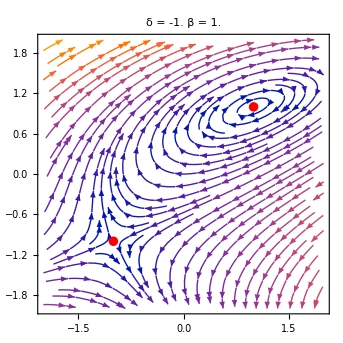

```mathematica
StreamPlot[F[u,v,-1,1],{u,-2,2},{v,-2,2},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{u,v}]/.NSolve[#==0&/@F[u,v,-1,1],{u,v}]),
PlotLabel->"δ = "<>ToString[N@-1]<>"  β = "<>ToString[N@1]
]
```

```mathematica
V[u_,v_]:=u^2+(v-1/2)^2
```

```mathematica
Dot[Grad[V[u,v],{u,v}],F[u,v,d,1]]//FullSimplify
```

v (-1+2 v)+u (1+2 d-2 u+2 v^2)

```mathematica
Manipulate[
StreamPlot[F[u,v,d,b],{u,-10,10},{v,-10,10},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{u,v}]/.NSolve[#==0&/@F[u,v,d,b],{u,v}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@b],ImageSize->Large
],{d,-5,5,0.01},{b,-5,5,0.01}
]
```

```mathematica
NSolve[{v^2+v-u+0.1==0,2v-u==0},{u,v}]
```

{{u→1.7746,v→0.887298},{u→0.225403,v→0.112702}}

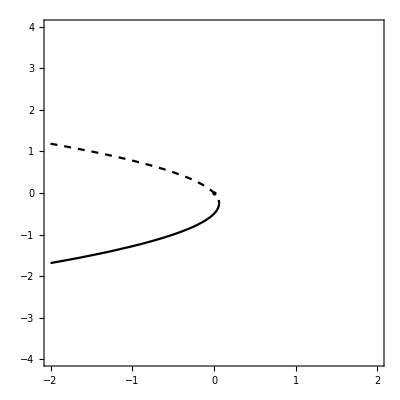

```mathematica
f1[v_,r_]:=v^2+v-v/2+r
λ=D[f1[x,r],x];
Show[ContourPlot[{ConditionalExpression[f1[x,r],λ<0]==0,ConditionalExpression[f1[x,r],λ>0]==0},{r,-2,2},{x,-4,4},ContourStyle->{{Black},{Black,Dashed}},
Epilog->{Point[{0,0}]}
]]
```

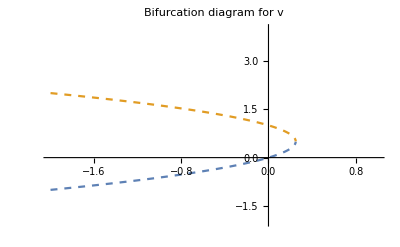

```mathematica
Plot[
{1/2(1-√(1-4d)),1/2(1+√(1-4d))},{d,-2,1},PlotStyle->Dashed,PlotLabel->"Bifurcation diagram for v",PlotRange->{{-2,1},{-2,4}}
]
```

```mathematica
ContourPlot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{b,-5,5},{d,-5,5}]
```

-Graphics-

```mathematica
ani=Animate[
Show[Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{d,-10,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->If[b<=1,{Dashed,Automatic},Dashed],PlotLabel->"u, b = "<>ToString[b]],
ParametricPlot[{(1-x)^2/4,(x(x-1))/2},{x,-10,10},PlotStyle->{Gray,Dotted}
]
]
,{b,-5,5}
]
```

```mathematica
Save["ani.gif",ani]
```

```mathematica
dat=Table[Show[Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{d,-10,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->Dashed,PlotLabel->"u, b = "<>ToString[b]],
ParametricPlot[{(1-x)^2/4,(x(x-1))/2},{x,-10,10},PlotStyle->{Gray,Dotted}
]
],{b,-5,5,0.1}];
Export["ani_u.gif",dat]
```

ani_u.gif

```mathematica
dat=Table[Show[Plot[{1/2(b-1-√((1-b)^2-4d)),1/2(b-1+√((1-b)^2-4d))},{d,-10,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->Dashed,PlotLabel->"v, b = "<>ToString[b]],
ParametricPlot[{(1-x)^2/4,(x-1)/2},{x,-10,10},PlotStyle->{Gray,Dotted}
]
],{b,-5,5,0.1}];
Export["ani_v.gif",dat]
```

ani_v.gif

```mathematica
Export["uv.png",ParametricPlot[{(b(b-1))/2,(b-1)/2},{b,-5,5},PlotLabel->"uv bifurcation point"]]
```

uv.png

```mathematica
Plot[]
```